A two-state Tsetlin Automaton is represented by a positive integer (representing the current state):

```mathematica
3
```

3

Approach is a helper function that takes three inputs,(x, y, t) and outputs x moved t closer to y (unless x==y, in which case x is outputted.

```mathematica
Approach[x_?NumberQ,y_?NumberQ,t_?NumberQ]:=
Which[
x==y,x,
x>y,x-t,
x<y,x+t]
```

```mathematica
Approach[3,6,1]
```

4

Most Tsetlin Automaton-related functions take at least the following two arguments as input: the state as well as the state identifier ( a number n such that the total number of states = 2n).

TsetlinAction is a function that takes a current state as well as a state identifier, and outputs a 1 or a 2 (useful for indexing) depending on how the current state compares to the state identifier.

```mathematica
TsetlinAction[t_Integer,si_Integer]:=
If[
t>si,
2,
1]
```

TsetlinPunish and TsetlinReward both take a state and a state identifier as input and punish/reward the Tsetlin automaton.

```mathematica
TsetlinPunish[t_Integer,si_Integer]:=
If[
t>si,
Approach[t,1,1],
Approach[t,2*si,1]]
```

```mathematica
TsetlinReward[t_Integer,si_Integer]:=
If[
t>si,
Approach[t,2*si,1],
Approach[t,1,1]]
```

```mathematica
TsetlinPunish[4,3]
```

3

```mathematica
TsetlinReward[4,3]
```

5

TsetlinUpdate takes a state, a state identifier, and a number n such that n∈{1,2} and updates the Tsetlin machine by rewarding it if it produced output equal to n, or punishing it if it did not. It then outputs the Tsetlin Automata.

```mathematica
TsetlinUpdate[t_Integer,si_Integer,n_Integer]:=
If[
TsetlinAction[t,si]==n,
TsetlinReward[t,si],
TsetlinPunish[t,si]]
```

Train a Tsetlin Automaton 10 times on a definite two-armed bandit problem.

```mathematica
definite2ArmBanditLearnList=NestList[ (* should learn 1, which always wins here *)
TsetlinUpdate[
#,
3,
Position[
#,
TakeLargestBy[#,#&,1]⟦1⟧]⟦1⟧⟦1⟧&@{1,0}]&,
3,10]
```

{3,2,1,1,1,1,1,1,1,1,1}

```mathematica
TsetlinAction[definite2ArmBanditLearnList[[-1]],3] (* outputs the final action choice of the automaton *)
```

1

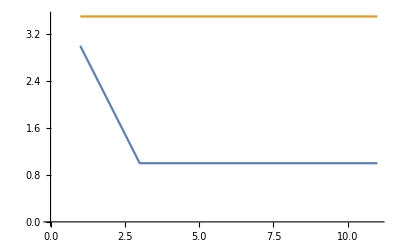

```mathematica
ListLinePlot[{definite2ArmBanditLearnList,Table[3.5,{x,definite2ArmBanditLearnList}] }] (* plot the learning curve of the automaton *)
```

Train a Tsetlin Automaton 10 times on an indefinite two-armed bandit problem.

```mathematica
indefinite2ArmBanditLearnList=NestList[ (* should learn 1, which usually (not always) wins here *)
TsetlinUpdate[
#,
3,
Position[
#,
TakeLargestBy[#,#&,1]⟦1⟧]⟦1⟧⟦1⟧&@{RandomVariate[NormalDistribution[0.75,.5]],RandomVariate[NormalDistribution[0.25,.5]]}]&,
4,10]
```

{4,5,4,3,2,1,2,1,1,1,2}

```mathematica
TsetlinAction[indefinite2ArmBanditLearnList[[-1]],3] (* outputs the final action choice of the automaton *)
```

1

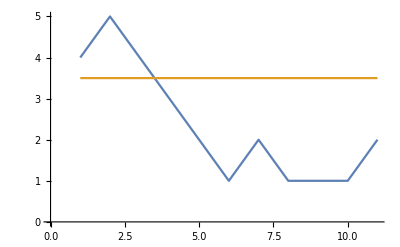

```mathematica
ListLinePlot[{indefinite2ArmBanditLearnList,Table[3.5,{x,indefinite2ArmBanditLearnList}] }](* plot the learning curve of the automaton *)
```

TsetlinWeightedReward rewards the Tsetlin Automaton depending on a probability based on s. This is important in a Tsetlin Machine.

```mathematica
TsetlinWeightedReward[t_Integer,si_Integer,s_?NumberQ]:=
If[
RandomReal[]≤((s-1)/s),
TsetlinReward[t,si],
t]
```

```mathematica
TsetlinWeightedReward[3,3,1]
```

3

```mathematica
TsetlinWeightedReward[3,3,1000]
```

2

TsetlinWeightedPunish is the punish equivalent of TsetlinWeightedReward.

```mathematica
TsetlinWeightedPunish[t_Integer,si_Integer,s_?NumberQ]:=
If[
RandomReal[]≤((s-1)/s),
TsetlinPunish[t,si],
t]
```